Piecewise[{{0, -∞<k<-10}, {k+10, -10≤k<0}, {10-k, 0≤k≤10}}]

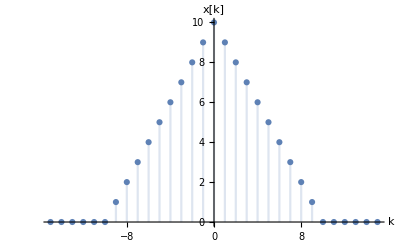

k | x[k]
-15 | 0
-14 | 0
-13 | 0
-12 | 0
-11 | 0
-10 | 0
-9 | 1
-8 | 2
-7 | 3
-6 | 4
-5 | 5
-4 | 6
-3 | 7
-2 | 8
-1 | 9
0 | 10
1 | 9
2 | 8
3 | 7
4 | 6
5 | 5
6 | 4
7 | 3
8 | 2
9 | 1
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0

\begin{array}{|l|r|}
\hline
 \text{k} & \text{x[k]} \\
\hline
 -15 & 0 \\
\hline
 -14 & 0 \\
\hline
 -13 & 0 \\
 -12 & 0 \\
 -11 & 0 \\
 -10 & 0 \\
 -9 & 1 \\
 -8 & 2 \\
 -7 & 3 \\
 -6 & 4 \\
 -5 & 5 \\
 -4 & 6 \\
 -3 & 7 \\
 -2 & 8 \\
 -1 & 9 \\
 0 & 10 \\
 1 & 9 \\
 2 & 8 \\
 3 & 7 \\
 4 & 6 \\
 5 & 5 \\
 6 & 4 \\
 7 & 3 \\
 8 & 2 \\
 9 & 1 \\
 10 & 0 \\
 11 & 0 \\
 12 & 0 \\
 13 & 0 \\
 14 & 0 \\
 15 & 0 \\
\end{array}

```mathematica
Clear["Global`*"]
T = 10;
x[k_] := Piecewise[{{0,-∞<k<-T},{k+T,-T<= k<0},{-k+T,0 <= k<= T},{0,T<k<∞}}]
datos = Table[{k,x[k]},{k,-(T+5),(T+5)}];
TraditionalForm[x[k]] 
DiscretePlot[x[k],{k,-(T+5),(T+5)},AxesLabel->{"k", "x[k]"}]
Grid[Prepend[datos,{"k","x[k]"}],Background->{None,{Lighter[Yellow,.9],
{White,Lighter[Blend[{Blue,Green}],.8]}}},
Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},
Darker[Gray,.6]},
{Darker[Gray,.6],
Darker[Gray,.6],
{False},Darker[Gray,.6]}},
Alignment->{{Left,Right,{Left}}},
ItemSize->{{10,5,3,3}},
Frame->Darker[Gray,.6],
ItemStyle->14,
Spacings->{Automatic,.8}]
TeXForm[%]
```